```mathematica
toBase60[x_]:=TakeDrop@@RealDigits[x,60]
```

```mathematica
fromBase60[d1_,d2_]:=FromDigits[d1,60]+FromDigits[d2,60]*60^-Length[d2]
```

```mathematica
zigzag[a_Association]/;!KeyExistsQ[a,"Translation"]:=zigzag[Append[a,"Translation"->0]]
```

```mathematica
zigzag[a:KeyValuePattern[{
"Min"->m_,
"Max"->M_,
"Slope"->d_,
"Initial"->{i_,increasing_}
}]]:=zigzag[Append[KeyDrop[a,"Initial"],"Translation"->(i-m)/d*If[increasing,1,-1]]]
```

```mathematica
zigzag[a:KeyValuePattern[{
"Min"->m_,
"Max"->M_,
"Slope"->d_,
"Translation"->t_
}]]["f"]:=Function[x,TriangleWave[{m,M},3/4+(t+x)*d/(M-m)/2]]
```

```mathematica
zigzag[KeyValuePattern[{"Min"->m_}]]["Min"]:=m
zigzag[KeyValuePattern[{"Max"->M_}]]["Max"]:=M
zigzag[KeyValuePattern[{"Slope"->d_}]]["Slope"]:=d
zigzag[KeyValuePattern[{"Translation"->t_}]]["Translation"]:=t
```

```mathematica
zz_zigzag["Period"]:=2*(zz["Max"]-zz["Min"])/zz["Slope"]
zz_zigzag["Initial"]:=zz["f"][0]
```

```mathematica
zigzag/:Min[zz_zigzag]:=zz["Min"]
zigzag/:Max[zz_zigzag]:=zz["Max"]
zigzag/:Mean[zz_zigzag]:=Mean[{zz["Min"],zz["Max"]}]
```

### Old

```mathematica
zigzag[{m_,M_},d_,i_,increasing_][x_]:=TriangleWave[{m,M},3/4+x*d/(M-m)/2]
zigzag[{m_,M_},d_,i_]:=zigzag[{m,M},d,i,True]
zigzag[{m_,M_},d_]:=zigzag[{m,M},d,0]
```

```mathematica
zigzagPeriod[zigzag[{m_,M_},d_,i_]]:=2*(M-m)/d
```

```mathematica
zigzag/:Mean[zigzag[{m_,M_},d_,i_]]:=Mean[{m,M}]
zigzag/:Min[zigzag[{m_,M_},d_,i_]]:=m
zigzag/:Max[zigzag[{m_,M_},d_,i_]]:=M
```

```mathematica
Clear[zigzag]
```

## Examples

```mathematica
zz=zigzag[{fromBase60[{28},{10,39,40}],fromBase60[{30},{1,59}]},fromBase60[{},{18}]];
```

```mathematica
zz=zigzag[<|
"Min"->fromBase60[{28},{10,39,40}],
"Max"->fromBase60[{30},{1,59}],
"Slope"->fromBase60[{},{18}],
"Initial"->{fromBase60[{28},{20,55,18}],False}
|>];
```

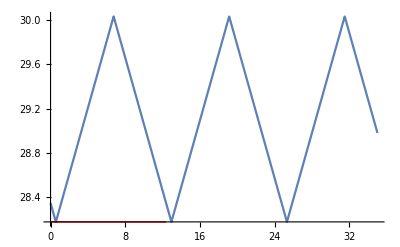

```mathematica
Plot[zz["f"][x],{x,0,35},Epilog->{Red,Line[{{0,Min[zz]},{zz["Period"],Min[zz]}}]}]
```

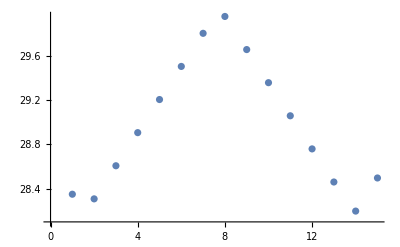

```mathematica
ListPlot[Table[zz["f"][x],{x,0,14}]]
```

```mathematica
A=Table[zz["f"][x],{x,0,14}];
```

```mathematica
B=Rest@FoldList[Plus,fromBase60[{18},{17,48,52}],A];
```

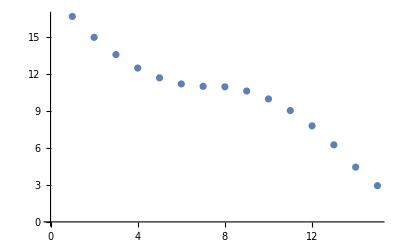

```mathematica
ListPlot[Mod[B,30]]
```

Page 188

```mathematica
Grid[Map[Apply[StringRiffle[#1,","]<>";"<>StringRiffle[#2,","]&]@*toBase60,Transpose[{A,Mod[B,30]}],{2}],Alignment->Left,Frame->All]
```

28;20,55,18 | 16;38,44,10
28;18,24,2 | 14;57,8,12
28;36,24,2 | 13;33,32,14
28;54,24,2 | 12;27,56,16
29;12,24,2 | 11;40,20,18
29;30,24,2 | 11;10,44,20
29;48,24,2 | 10;59,8,22
29;57,33,58 | 10;56,42,20
29;39,33,58 | 10;36,16,18
29;21,33,58 | 9;57,50,16
29;3,33,58 | 9;1,24,14
28;45,33,58 | 7;46,58,12
28;27,33,58 | 6;14,32,10
28;11,45,22 | 4;26,17,32
28;29,45,22 | 2;56,2,54

```mathematica
zz1=zigzag[<|
"Min"->fromBase60[{28},{10,39,40}],
"Max"->fromBase60[{30},{1,59}],
"Slope"->fromBase60[{},{18}]
|>];
zz2=zigzag[<|
"Min"->fromBase60[{28},{10,40}],
"Max"->fromBase60[{30},{2}],
"Slope"->fromBase60[{},{18}]
|>];
```

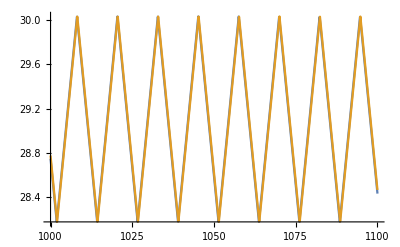

```mathematica
Plot[{zz1["f"][x],zz2["f"][x]},{x,1000,1100}]
```

```mathematica
FullSimplify[zz1["f"][x]-zz2["f"][x]]
```

TriangleWave[{304319/10800,108119/3600},3/4+(810 x)/10019]-TriangleWave[{1268/45,901/30},3/4+(27 x)/334]

```mathematica
ContinuedFraction@zz1["Period"]
```

{12,2,1,2,2,3,2,5}

```mathematica
FromContinuedFraction[{12,2,1,2,2}]
```

235/19

```mathematica
ContinuedFraction@zz2["Period"]
```

{12,2,1,2,3}

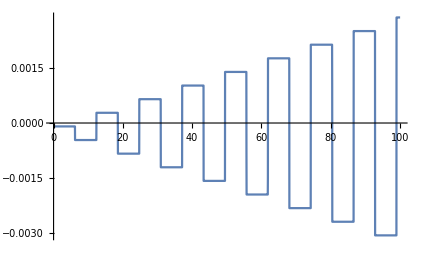

```mathematica
Plot[zz1["f"][x]-zz2["f"][x],{x,0,100}]
```

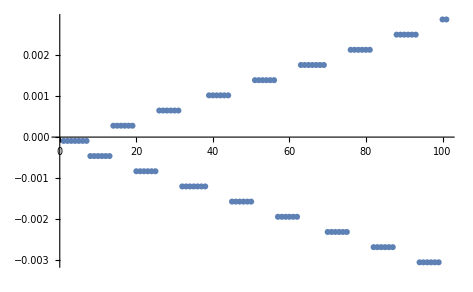

```mathematica
ListPlot[Table[zz1["f"][x]-zz2["f"][x],{x,0,100}]]
```

```mathematica
zz1["f"][x]
```

TriangleWave[{304319/10800,108119/3600},3/4+(810 x)/10019]

```mathematica
zz2["f"][x]
```

TriangleWave[{1268/45,901/30},3/4+(27 x)/334]